# Kalman Folding versus Particle Filtering

Brian Beckman
16 Mar 2018

## Abstract

Kalman Folding is equivalent to Renormalized Recurrent Least Squares, and is Bayesian by construction (Beckman, 2018, https://goo.gl/CwLYjf). Therefore, it regularizes well. Sticking with concrete, numerical examples, we show that particle filtering can reproduce the results of Kalman Folding. For a more theoretical analysis, see Fernández-Villaverde (http://www.ssc.upenn.edu/~jesusfv/filters_format.pdf).

## Bishop’s Example

Chris Bishop’s Pattern Recognition and Machine Learning has an extended example fitting higher-order polynomials, linear in their coefficients, starting in section 1.1.

Bishop’s Training Set

Create a sequence of Ν=10 inputs for a training set, equally spaced in [0..1].

```mathematica
ClearAll[bishopTrainingSetX];
bishopTrainingSetX[Ν_]:=Array[Identity,Ν,{0.,1.}];
```

Bishop’s ground truth is a single cycle of a sine wave. Add noise to a sample taken at the inputs of the training set above. Bishop doesn’t state an observation noise, but I guess σ_z=σ_t=0.30 to create a fake data set that resembles Bishop’s qualitatively.

Wolfram’s built-in NormalDistribution takes the standard deviation as its second argument, not the variance. Mixing up standard deviation and variance is an easy mistake. Bishop’s notation for normal distribution takes variance as second argument, so beware.

```mathematica
ClearAll[bishopTrainingSetY,bishopGroundTruthY];
bishopGroundTruthY[xs_]:=Sin[2.π#]&/@xs;
bishopTrainingSetY[xs_,σ_]:=
With[{n=Length@xs},
bishopGroundTruthY[xs]
+RandomVariate[NormalDistribution[0.,σ],n]];
```

Take a sample of the outputs and assign it the names bts for bishopTrainingSet. It isn’t his actual training set, which I didn’t find in print, just my simulation.

```mathematica
ClearAll[bishopTrainingSet,bts,bishopFake,bishopFakeSigma];
bishopFake[n_,σ_]:=
With[{xs=bishopTrainingSetX[n]},
With[{ys=bishopTrainingSetY[xs,σ]},
{xs,ys}]];
bishopFakeSigma=0.30;
bishopTrainingSet=bts=bishopFake[10,bishopFakeSigma];
```

Make a plot like Bishop’s figure 1.7 (page 10).

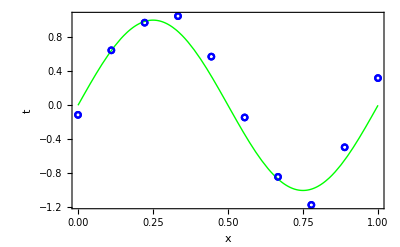

```mathematica
With[{lp=ListPlot[btsᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Show[{lp,(* once to set the scale *)
Plot[Sin[2.π x],{x,0.,1.},PlotStyle->{Thick,Green}],
lp (* again to overdraw the plot *)},
Frame->True,
FrameLabel->{"x","t"}]]
```

Partials: Gradients of the Unknown Parameters

Write a function for partials.

```mathematica
ClearAll[partialsFn];
partialsFn[order_,xs_]:=
Transpose@Quiet@Table[#^(i-1)/.{Indeterminate->1},{i,order+1}]&@xs;
```

A convenience function:

```mathematica
ClearAll[symbolicPowers];
symbolicPowers[variable_,order_]:=
partialsFn[order,{variable}]⟦1⟧;
```

```mathematica
ClearAll[rlsUpdate];
rlsUpdate[sqrtPΖ_][{ξ_,Λ_},{ζ_,a_}]:=
With[{sPΖia=LinearSolve[sqrtPΖ,a]},
With[{Π=(Λ+sPΖiaᵀ.sPΖia)},
{LinearSolve[Π,(sPΖiaᵀ.ζ+Λ.ξ)],Π}]];
```

```mathematica
ClearAll[rrlsFit];
rrlsFit[σ2ζ_,σ2ξ_][Μ_,trainingSet_]:=
With[{xs=trainingSet⟦1⟧,ys=trainingSet⟦2⟧},
With[{ξ0=List/@ConstantArray[0,Μ+1],
Λ0=σ2ξ^-1*IdentityMatrix[Μ+1]},
Module[{ξ,Λ},
{ξ,Λ}=Fold[
rlsUpdate[√σ2ζ IdentityMatrix[1]],
{ξ0,Λ0},
{List/@ys,List/@partialsFn[Μ,xs]}ᵀ];
{ξ/√σ2ζ,Λ}]]];
```

```mathematica
ClearAll[goodSolution];
```

```mathematica
Manipulate[Module[{x},
With[{σζ2=10.^(2logσζ),σξ2=10.^(2logσξ)},
With[{rrls=Quiet@rrlsFit[σζ2,σξ2][Μ,bts]},
<|"σζ2"->σζ2,"σξ2"-> σξ2,"rrls⟦1⟧"->MatrixForm[goodSolution=rrls⟦1⟧]|>
]]],
Column[{
Button["RESET",(Μ=9;logσξ=.5;logσζ=-1.5)&],
Control[{{Μ,9,"order Μ"},0,16,1,Appearance->{"Labeled"}}],Control[{{logσξ,.5,"log σξ (KAL)"},-3, 5,Appearance->"Labeled"}],
Control[{{logσζ,-1.5,"log σζ (KAL)"},-7,3,Appearance->"Labeled"}]}]]
```

```mathematica
Dynamic[goodSolution]
```

```mathematica
Manipulate[Module[{x},
With[{
terms=symbolicPowers[x,Μ],
cs=ϕ[Μ]/@List/@bts⟦1⟧,
ts=bts⟦2⟧,
σζ2=10.^(2logσζ),σξ2=10.^(2logσξ)},
With[{rrls=Quiet@rrlsFit[σζ2,σξ2][Μ,bts]},
With[{rrlsFn={terms}.rrls⟦1⟧},
With[{lp=ListPlot[btsᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Module[{showlist={lp,Plot[Sin[2.π x],{x,0.,1.},PlotStyle->{Thick,Green}]}},
AppendTo[showlist,Plot[rrlsFn,{x,0,1},PlotStyle->{Purple}]];Quiet@Show[showlist,Frame->True,ImageSize->Medium,FrameLabel->{{"ζ",""},{"ξ",Grid[{{"α: ",α,"β:",β}}]
}}]]]]]]],
Column[{
Button["RESET",(Μ=4;logσξ=.5;logσζ=-1.5)&],
Control[{{Μ,4,"order Μ"},0,16,1,Appearance->{"Labeled"}}],Control[{{logσξ,.5,"log σξ"},-3, 5,Appearance->"Labeled"}],
Control[{{logσζ,-1.5,"log σζ"},-7,3,Appearance->"Labeled"}]}]]
```

## Particle Filter

Each particle ξ^i,i∈[1.. N_s], is an (Μ+1)-vector guess at the state, i.e., the column vector of coefficients. There are N_s of them for each time tick in the simulation.

Initialization

```mathematica
ClearAll[σ0,P,P0,ξ0,ξ0s,importanceFunction];
ClearAll[Ns,σ0,σ,ξ,importanceFunctions,ξs,Μ,ws];

Ns=1000;

Μ=9;

σ0=10;
σ[0]=List/@ConstantArray[σ0,Μ+1];

ξ[0]=List/@ConstantArray[0.,Μ+1];

importanceFunctions[t_]:=
Table[
NormalDistribution[ξ[t]⟦i,1⟧,σ[t]⟦i,1⟧],
{i,Μ+1}];

ξs[0]=
Table[
ξ[0]⟦i,1⟧+RandomVariate[importanceFunctions[0]⟦i⟧],
{i,Μ+1},{j,Ns}];

Print[<|"σ"->σ,"Dimensions[ξs[0]]"->Dimensions[ξs[0]]|>];

ws[0]=ConstantArray[1./Ns,Ns];
Plus@@ws[0]
```

<|σ→σ,Dimensions[ξs[0]]→{10,1000}|>

1.

3D Point Clouds

```mathematica
ClearAll[threeDPointClouds];
threeDPointClouds[ξs_,σ_]:=
DynamicModule[{i=1,j=2,k=3},
Manipulate[Graphics3D[Point/@({ξs⟦i,All⟧,ξs⟦j,All⟧,ξs⟦k,All⟧}ᵀ),
Axes->True,AspectRatio->1,
AxesLabel->{"i: "<>ToString[i],"j: "<>ToString[j],"k: "<>ToString[k]},PlotRange->3{{-σ,σ},{-σ,σ},{-σ,σ}}],
Grid[{
{"i",SetterBar[Dynamic[i],Range[Μ+1]]},
{"j",SetterBar[Dynamic[j],Range[Μ+1]]},
{"k",SetterBar[Dynamic[k],Range[Μ+1]]}}]]];
threeDPointClouds[ξs[0],σ0]
```

Observations and Residuals

Observations are constant with time, but we include a time parameter for generality. The particle cloud changes with time due to resampling.

```mathematica
ClearAll[ξcol];
ξcol[t_,n_/;(1≤n≤Ns)]:=List/@ξs[t]⟦All,n⟧;
```

```mathematica
ClearAll[ζcol];
ζcol[t_]:=List/@bts⟦2⟧
```

```mathematica
ClearAll[residuals];
residuals[t_,n_/;1≤n≤Ns]:=
partialsFn[Μ,bts⟦1⟧].ξcol[t,n]-ζcol[t];
```

Sum of Squared Residuals (SSR)

```mathematica
ClearAll[ssr];
ssr[t_,n_/;1≤n≤Ns]:=(residuals[t,n]ᵀ.residuals[t,n])⟦1,1⟧;
```

```mathematica
ClearAll[ssrs];
(ssrs=ssr[0,#]&/@Range[Ns])//Short
```

{637.795,237.003,«996»,824.996,4337.9}

New Weights

Larger SSR means further from the observations. Let weights be inversely proportional to SSR, with divide-by-zero intentionally faulting because a zero SSR would signal an extremely improbable situation, most likely a bug somewhere else in the software.

```mathematica
(ws[1]= 1/ssrs/Plus@@(1/ssrs))//Short[#,3]&
```

{0.000853839,0.00229775,0.0000858845,0.000252737,«992»,0.000550557,0.0000953933,0.000660094,0.000125539}

Check:

```mathematica
Plus@@ws[1]
```

1.

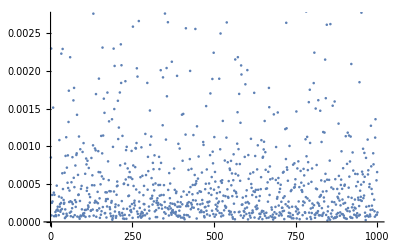

```mathematica
ListPlot[ws[1]]
```

Cull Particles

Keep only the particles that “do well” for the next time step, by some criterion driven by hyperparameters.

Pair each particle with its index:

```mathematica
ClearAll[indexedWeights];
(indexedWeights=MapThread[List,{Range[Ns],ws[1]}])//Short
```

{{1,0.000853839},«998»,{1000,0.000125539}}

Keep the top p%. In general, p should be the reciprocal of an integer that divides N_s because we are going to copy each survivor 1/p times to make a new sample of size N_s.

```mathematica
ClearAll[p,sortedIndexedWeights,topPWeights,topPIndexedWeights,topPIndices,topPParticles];
p=0.10;
<|"sortedIndexedWeights"->((sortedIndexedWeights=Reverse@SortBy[indexedWeights,Last])//Short),
"topPIndexedWeights"->((topPIndexedWeights=sortedIndexedWeights⟦;;Floor[p Ns]⟧)//Short),
"topPWeights"->((topPWeights=Last/@topPIndexedWeights)//Short),
"topPIndices"->((topPIndices=First/@topPIndexedWeights)//Short),
"topPParticles//Dims"->((topPParticles=(ξs[0]⟦All,#⟧&/@topPIndices)ᵀ)//Dimensions),
"top 3 Particles"->(topPParticles⟦All,1;;3⟧//MatrixForm)|>
```

<|sortedIndexedWeights→{{804,0.0327154},«998»,{847,0.0000188323}},topPIndexedWeights→{{804,0.0327154},«98»,{840,0.00215104}},topPWeights→{0.0327154,0.0268483,«97»,0.00215104},topPIndices→{804,740,586,291,294,269,736,609,440,164,122,«78»,159,2,193,37,807,499,33,573,60,565,840},topPParticles//Dims→{10,100},top 3 Particles→(1.64507 | 0.555848 | -3.00641
-2.02778 | 0.695253 | 11.7577
-0.681058 | -0.501834 | -2.55939
3.86676 | -5.21696 | -9.81486
0.751128 | 0.381881 | -6.89924
1.07967 | -16.6291 | 9.43933
-9.23144 | 9.87651 | -4.70284
14.4863 | 13.0525 | 2.61115
-13.0477 | -6.74595 | 10.96
3.72471 | 1.83075 | -6.68278)|>

Structure emerges after culling.

```mathematica
threeDPointClouds[topPParticles,σ0]
```

Top p Particles

Replace each particle with 1/p copies, each perturbed by this new σ_1. There are other ways to compute an importance sample of the top p particles. One way, possibly biased, is to keep the original survivor and add 1/p-1 perturbed copies. We first perform this latter sample (original joined to three copies) to check matrix dimensions, but proceed with the former sample (four copies).

### Standard Deviations

```mathematica
ClearAll[σξ];
σξ[1]=StandardDeviation/@topPParticles
```

{3.64965,8.22725,8.44334,9.42344,9.69971,10.3303,9.7279,8.16962,9.15821,9.56692}

```mathematica
ClearAll[conjColumns];
conjColumns[m1_,m2_]:=((m1ᵀ)~Join~(m2ᵀ))ᵀ;
```

### Unbiased? Importance Sample

```mathematica
ClearAll[make1OverP];
make1OverP[ξ_,σξ_,p_]:=
With[{n=Floor[1/p]},
Table[
RandomVariate[NormalDistribution[ξ⟦m⟧,σξ⟦m⟧],n],
{m,Μ+1}]];
make1OverP[topPParticles⟦All,41⟧,σξ[1],p]//MatrixForm
```

(8.80296 | 0.740502 | 4.02662 | 6.71818 | 4.4175 | 1.75667 | 5.16325 | 2.90578 | 4.03013 | 5.94944
-20.9798 | -7.22437 | 1.16919 | -15.3904 | -20.4799 | -21.5674 | -23.9785 | -5.12209 | -5.8984 | -12.2151
-8.31574 | -5.78303 | -27.56 | 1.34088 | -16.8589 | -19.4032 | -13.3302 | -13.8891 | -22.3105 | 6.6617
-10.9862 | -4.23829 | 35.3368 | -1.40484 | -2.04017 | 15.5958 | 4.3734 | 19.6574 | 1.89909 | 8.26312
10.139 | 10.8937 | -7.27831 | 18.295 | 15.0967 | 7.38342 | 7.3509 | 21.1331 | 10.9387 | 2.59328
7.76449 | 4.2914 | 11.4186 | 7.58039 | 4.76365 | 11.8593 | 14.7903 | 2.93488 | -8.34596 | -3.48769
1.61621 | 4.81461 | -4.45432 | -8.1775 | -14.5998 | -23.6793 | -11.0863 | -11.9205 | 5.82907 | -8.89001
-10.1498 | 8.07481 | -0.0976447 | -7.17417 | -8.02084 | 0.834168 | 14.1881 | 11.551 | 1.5956 | 6.4105
4.87064 | 3.34198 | 0.0466664 | 5.52504 | 11.9145 | 2.55942 | 4.73685 | -1.10975 | 1.28283 | -10.4874
4.73453 | 25.2507 | -35.6894 | 0.165484 | 14.4847 | -7.51728 | -13.0636 | 6.83458 | -9.10515 | 10.871)

New Particle Cloud

```mathematica
topPParticles//Dimensions
```

{10,100}

```mathematica
(ξs[1]=Fold[conjColumns,make1OverP[#,σξ[1],p]&/@(topPParticlesᵀ)])//Dimensions
```

{10,1000}

```mathematica
threeDPointClouds[ξs[1],σ0]
```

```mathematica
StandardDeviation/@ξs[0]
```

{10.0356,10.2049,10.3623,10.3634,10.3313,10.0132,9.91126,10.0487,10.2828,10.1863}

```mathematica
StandardDeviation/@ξs[1]
```

{5.00288,11.6045,12.2,12.9966,13.9464,14.7417,13.7275,11.4756,13.179,13.2525}

Package and Experiment

Abstract the procedures above and iterate.

We have some global variables, namely Μ and N_s. Assert that input dimensions match expectations w.r.t. these globals.

Add a regularization parameter, λ, to penalize particles of large norm.

```mathematica
ClearAll[ssrFn,scalar,regula,weights,cull,iterate];
On[Assert];
scalar[m_]:=(
Assert[{1,1}===Dimensions[m]];
m⟦1,1⟧);
ssrFn[A_,ζ_]:=
Function[ξ,
With[{ress=ζ-A.ξ},
With[{ssr=ressᵀ.ress},
ssr]]];
regula[λ_][ξ_]:=(λ(ξ.ξ));
weights[xs_,ζ_,λ_][ξs_]:=
With[{A=partialsFn[Μ,xs]},
(Assert[Μ+1===Length[xs]];
Assert[Μ+1===Length[ζ]];
Assert[{Μ+1,Ns}===Dimensions[ξs]];
With[{cost=(regula[λ]/@(ξsᵀ))+(scalar/@ssrFn[A,ζ]/@(ξsᵀ))},
With[{ws= 1/cost/Plus@@(1/cost)},
Assert[Ns===Length[ws]];
Assert[Round[Plus@@ws,10.^-6]===1.];
ws]])];
cull[xs_,ζ_,λ_][p_,ξs_]:=Module[{indexedWeights,sortedIndexedWeights,topPIndexedWeights,topPWeights,topPIndices,topPParticles},
indexedWeights=Function[ws,MapThread[List,{Range[Ns],ws}]];
sortedIndexedWeights=Function[ws,Reverse@SortBy[indexedWeights[ws],Last]];
topPIndexedWeights=Function[ws,sortedIndexedWeights[ws]⟦;;Floor[p Ns]⟧];
topPIndices=Function[ws,First/@topPIndexedWeights[ws]];
topPParticles=Function[ws,
With[{result=(ξs⟦All,#⟧&/@topPIndices[ws])ᵀ},
Assert[{Μ+1,Floor[p Ns]}===Dimensions[result]];
result]];
topPParticles[weights[xs,ζ,λ][ξs]]];
iterate[xs_,ζ_,λ_][p_,ξs_]:=
With[{culled=cull[xs,ζ,λ][p,ξs]},
With[{σξ=StandardDeviation/@culled},
With[{result=Fold[conjColumns,make1OverP[#,σξ,p]&/@(culledᵀ)]},
Assert[{Μ+1,Ns}===Dimensions[result]];
result]]];
```

```mathematica
ClearAll[looseThreeDPointClouds];
looseThreeDPointClouds[ξs_]:=
DynamicModule[{i=1,j=2,k=3},
Manipulate[Graphics3D[Point/@({ξs⟦i,All⟧,ξs⟦j,All⟧,ξs⟦k,All⟧}ᵀ),
Axes->True,AspectRatio->1,
AxesLabel->{"i: "<>ToString[i],"j: "<>ToString[j],"k: "<>ToString[k]}],
Grid[{
{"i",SetterBar[Dynamic[i],Range[Μ+1]]},
{"j",SetterBar[Dynamic[j],Range[Μ+1]]},
{"k",SetterBar[Dynamic[k],Range[Μ+1]]}}]]];
```

```mathematica
ClearAll[experiment];
(experiment=
Fold[
iterate[bts⟦1⟧,List/@bts⟦2⟧,0.75][p,#1]&,
ξs[0],Range[200]])//looseThreeDPointClouds
```

```mathematica
Manipulate[
With[{topFive=
cull[bts⟦1⟧,List/@bts⟦2⟧,0.75][0.005,
Fold[iterate[bts⟦1⟧,List/@bts⟦2⟧,λ][p,#1]&,ξs[0],Range[200]]]},
Module[{x},
With[{terms=symbolicPowers[x,Μ]},
With[{lp=ListPlot[btsᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Module[{showlist={lp,Plot[Sin[2.π x],{x,0,1},PlotStyle->{Thick,Green}]}},
AppendTo[showlist,Plot[{terms}.goodSolution,{x,0,1},PlotStyle->{Purple}]];
AppendTo[showlist,Plot[terms.topFiveᵀ⟦#⟧&/@Range[5],{x,0,1}]];
Show[showlist,Frame->True,ImageSize->Medium,FrameLabel->{{"z",""},{"x",""}}]]]]]],
{{λ,1.00},0.0,1.0,0.10,Appearance->{"Open","Labeled"}}]
```

## Conclusion